# Model of the NF-κB signaling module

©2002 Johns Hopkins University, California Institute of Technology
revised 1/4/2012 BES for Mathematica 8 and xlr8r 0.83 compatibility (original generated using Cellerator version 1.3.0303)

Model Courtesy of Andre Levchenko, Jonhs Hopkins University

References: 
1. Hoffmann, A.,* Levchenko, A.,* Scott, M.L., Baltimore, D. THe IkappaB-NF-kappaB signaling module:temporal control and selective gene activation. Science, 298: 1241, 2002

```mathematica
<<xlr8r.m
```

xCellerator 0.88 (21-July-2012) loaded 23 August 2012 at 16:21 GMT-06:60 using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4) (MathSBML 1203-002)
GNU General Public License (GPL) Terms Apply.

Generate the reactions for the NF-κB signaling module

```mathematica
circuit={{IkBa + NFkB⇄ IkBa$NFkB , a1, d1},{IKK$IkBa + NFkB⇄ IKK$IkBa$NFkB , a2, d2},{NFkB⇄NFkBn,tr1,tr2},{IkBa$NFkB->NFkB, deg1},{IkBan + NFkBn⇄ IkBan$NFkBn , a1, d1},{IKK+IkBa⇄IKK$IkBa,a3,d3},{IkBat->∅,deg3},{IkBa⇄IkBan,tr3,tr4},{IKK$IkBa$NFkB->IKK+NFkB,k1},{IKK$IkBa->IKK,k2},{IkBat↦IkBa,hill[vmax->0.8 3.06,khalf->10]},{IkBa$NFkB⇄IkBan$NFkBn,tr5,tr6},{IkBa->∅,deg2},{NFkBn↦IkBat,hill[vmax->0.83 1.2375,nhill->2,khalf->1]},{∅->IkBat,trb},{IKK+IkBa$NFkB⇄IKK$IkBa$NFkB , a4,d4},{IKK->∅,adapt}};
```

```mathematica
systemOfODEs=interpret[circuit];
```

Assign values to the rate constants

From reference (1)

```mathematica
systemConstants={
a1-> 30, a2-> 30, a3-> 1.35, a4-> 11.1,
tr1-> 5.4, tr2-> 0.0048, tr3-> 0.018, tr4-> 0.012,tr5-> 0, tr6-> 0.82944,
d1-> 0.03, d2-> 0.03, d3-> 0.0075, d4-> 0.105 ,
deg1-> 0.5 * 0.0027, deg2-> 0.5*0.0135, deg3-> 0.0168,
k1-> 1.221, k2-> 0.2442, trb-> 0.65*0.00014175, adapt-> 0.0072};
```

```mathematica
initialState={NFkB-> 0.003053, IkBa-> 0.372, IkBa$NFkB->0.09826,
NFkBn->.00047638,
IkBan->0.11937,
IkBan$NFkBn->0.001985,
IKK-> 0.1,
IkBat->0.008454217};
```

```mathematica
timeCourse=run[circuit,
initialConditions-> initialState,
rates-> systemConstants,
timeSpan-> 500,
verbose-> True]
```

{{IkBa→InterpolatingFunction[{{0.,500.}},<>],IkBan→InterpolatingFunction[{{0.,500.}},<>],IkBan$NFkBn→InterpolatingFunction[{{0.,500.}},<>],IkBat→InterpolatingFunction[{{0.,500.}},<>],IkBa$NFkB→InterpolatingFunction[{{0.,500.}},<>],IKK→InterpolatingFunction[{{0.,500.}},<>],IKK$IkBa→InterpolatingFunction[{{0.,500.}},<>],IKK$IkBa$NFkB→InterpolatingFunction[{{0.,500.}},<>],NFkB→InterpolatingFunction[{{0.,500.}},<>],NFkBn→InterpolatingFunction[{{0.,500.}},<>]}}

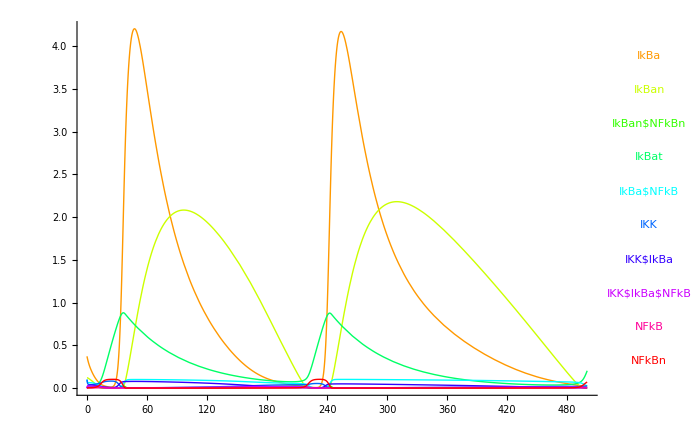
```mathematica
{{IkBa->InterpolatingFunction[{{0.,500.}},"<>"],-Graphics-IkBan->InterpolatingFunction[{{0.,500.}},"<>"],IkBan$NFkBn->InterpolatingFunction[{{0.,500.}},"<>"],IkBat->InterpolatingFunction[{{0.,500.}},"<>"],IkBa$NFkB->InterpolatingFunction[{{0.,500.}},"<>"],IKK->InterpolatingFunction[{{0.,500.}},"<>"],IKK$IkBa->InterpolatingFunction[{{0.,500.}},"<>"],IKK$IkBa$NFkB->InterpolatingFunction[{{0.,500.}},"<>"],NFkB->InterpolatingFunction[{{0.,500.}},"<>"],NFkBn->InterpolatingFunction[{{0.,500.}},"<>"]}}
```

```mathematica
runPlot[timeCourse, ImageSize-> 700]
```

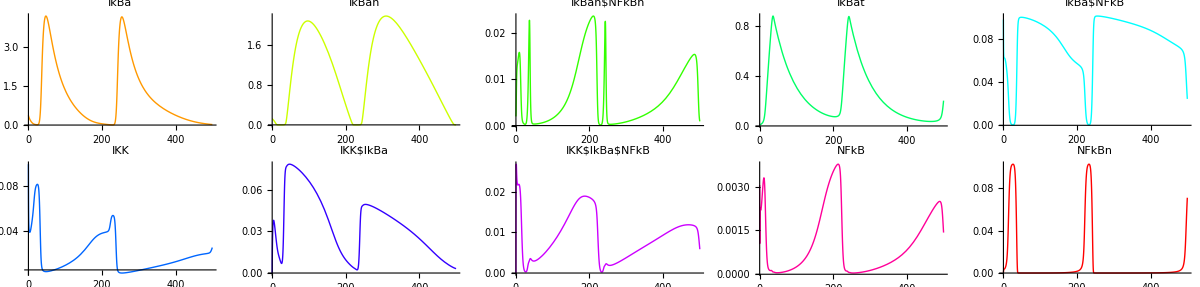

```mathematica
gridPlot[timeCourse, plotColumns-> 5, ImageSize-> 1200]
```

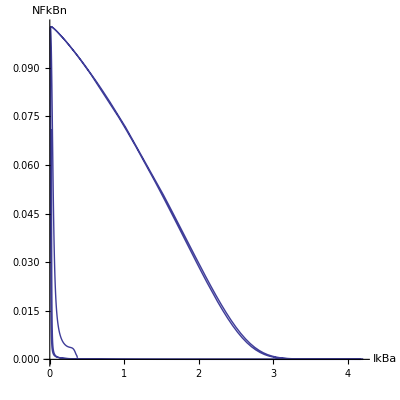

```mathematica
PhasePlot[timeCourse,{IkBa,NFkBn} ,{0,500}, AspectRatio-> 1, PlotRange-> All]
```